```mathematica
sol = DSolve[{y''[x] + λ*y[x] == 0, y'[0]==0, y'[1]==0}, y[x],x]
```

{{y[x]→Piecewise[{{C[1] Cos[x √λ], n∈ℤ&&n≥0&&λ==n^2 π^2}, {0, True}}]}}

```mathematica
eigfuns = Table[sol //.{n-> i, λ-> (Pi*n)^2}/.{C[1] -> 1},{i,5}]
```

{{{y[x]→Piecewise[{{Cos[π x], n∈ℤ&&n≥0&&π^2==n^2 π^2}, {0, True}}]}},{{y[x]→Piecewise[{{Cos[2 π x], n∈ℤ&&n≥0&&4 π^2==n^2 π^2}, {0, True}}]}},{{y[x]→Piecewise[{{Cos[3 π x], n∈ℤ&&n≥0&&9 π^2==n^2 π^2}, {0, True}}]}},{{y[x]→Piecewise[{{Cos[4 π x], n∈ℤ&&n≥0&&16 π^2==n^2 π^2}, {0, True}}]}},{{y[x]→Piecewise[{{Cos[5 π x], n∈ℤ&&n≥0&&25 π^2==n^2 π^2}, {0, True}}]}}}

```mathematica
eigfuns[[1,1,1,2]]
```

Piecewise[{{Cos[π x], n∈ℤ&&n≥0&&π^2==n^2 π^2}, {0, True}}]

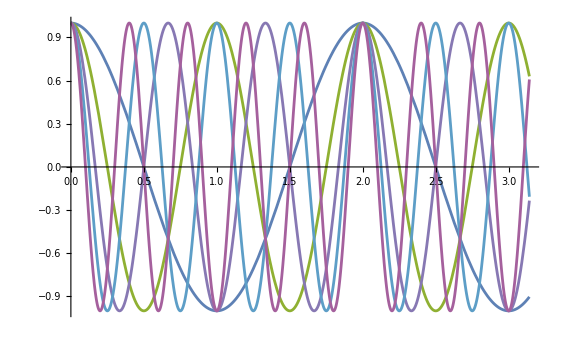

```mathematica
Plot[Evaluate[eigfuns[[All,1,1,2,1]]],{x,0,Pi}]
```

```mathematica
Ort
```